-Graphics-

# New in Wolfram Language 12.2

## Image, Audio and Video Updates

## Outline

Video Generation

Video Processing

Video Analysis

Video Editing

AnimatedImage

Improved Face Functionality

Image Scopes

And more

## Video Object—Recap (New in 12.1)

Version 12.1 of the Wolfram Language™ introduced the Video object as a new first-class citizen.

Version 12.2 extends the video functionalities to more editing, processing, analysis and generation.

The Video object is completely out-of-core.

Supports an extensive list of containers and codecs.

Bundled with complete stacks for image and audio processing.

Bundled with powerful machine learning and neural nets.

Bundled with statistics, visualization and many more capabilities.

The Video object as well as all video functions is “Experimental” until there is an in-notebook player and a more complete set of functions.

### A Quick Look

```mathematica
Video[file]
Video[url]
```

Construct a Video object:

```mathematica
v=Video["ExampleData/Caminandes.mp4"]
```

```mathematica
Information[v]
```

Extract video properties and parts:

```mathematica
Duration[v]
```

```mathematica
VideoFrameList[v,5]
```

```mathematica
Audio[v]
```

```mathematica
Audio[v]//Spectrogram
```

#### Codec Support

Install FFmpeg Version 4.0.0 or higher to get a more complete codec support. See the following for platform-specific instructions. With FFmpeg installed, the Wolfram Language™ makes use of it by default.

Check system options for video processing:

```mathematica
SystemOptions["VideoProcessingOptions"]
```

{VideoProcessingOptions→{TryUsingSystemFFmpeg→True}}

Number of supported video decoders:

```mathematica
Length/@$VideoDecoders
```

<|AVI→141,Matroska→237,MP4→21,Ogg→1,QuickTime→63,VideoFormat→259|>

See these Wolfram Community™ posts for instructions on how to install FFmpeg on different platforms:

Windows: https://community.wolfram.com/groups/-/m/t/2177967

macOS: https://community.wolfram.com/groups/-/m/t/2189614

Linux: https://community.wolfram.com/groups/-/m/t/2189622

## Video Generation

In Version 12.1, Export to video formats such as "MP4" was added or significantly updated. In addition to exporting and transcoding an existing video to a new file with specified parameters, one could generate new video content from Manipulate expressions or a list of images.

Version 12.2 introduces VideoGenerator, which writes frames and audio samples to a file as they are being generated. This allows for:

one-step frame generation and encoding

long video generation

```mathematica
VideoGenerator[func]
VideoGenerator[func, dur]
```

### Simple Examples

```mathematica
i=ResourceData["Sample Image: White Dog on a Beach"]
```

Video of a single image:

```mathematica
VideoGenerator[i,Quantity[2, "Seconds"]]
```

Video of a list of images with rotating color channels:

```mathematica
VideoGenerator[NestList[ImageApply[RotateLeft,#]&,i,2],Quantity[2, "Seconds"]]
```

Video of a rotating image:

```mathematica
VideoGenerator[ImageRotate[i,# π,Full]&,Quantity[2, "Seconds"]]
```

### More Examples

#### Video of a dynamically updating plot

```mathematica
VideoGenerator[Plot[Sin[4*# x],{x,0,10},]&,Quantity[2, "Seconds"]]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoGenerator-03203f08-e920-4a91-830c-b84372bbe187.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoGenerator-03203f08-e920-4a91-830c-b84372bbe187.mp4Thumbnail1StandardForm

#### Video of a rotating 3D object

Import and render a 3D object:

```mathematica
g=ExampleData[{"Geometry3D","Horse"}][[1,2]];
Graphics3D[{EdgeForm[],g},SphericalRegion->True,Boxed->False]
```

Generate a video of the 3D object rotating around the z axis:

```mathematica
horse=VideoGenerator[Graphics3D[{EdgeForm[],GeometricTransformation[g,RotationTransform[2π/2 #,{0,0,1}]]},]&,2,RasterSize->300,FrameRate->10]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoGenerator-9dbafbd5-cdd3-4971-91ef-09158d8a7e06.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoGenerator-9dbafbd5-cdd3-4971-91ef-09158d8a7e06.mp4Thumbnail1StandardForm

#### Rule 30

Generating frames from evolution of rule 30:

```mathematica
steps=128;
dims={width,height}={2*steps-1,steps};
```

```mathematica
t=Table[ImageResize[ColorNegate@ImageCrop[Image[CellularAutomaton[30,{{1},0},Floor[n]]],dims,Top],Scaled[2],Resampling->"Nearest"],{n,0,steps,1}];
```

```mathematica
VideoGenerator[t,2]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoGenerator-9355a53d-09b8-4292-ad26-d6ccf5f734a4.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoGenerator-9355a53d-09b8-4292-ad26-d6ccf5f734a4.mp4Thumbnail1StandardForm

Include the rule 30 audio:

```mathematica
a=Audio["ExampleData/rule30.wav"];
VideoGenerator[<|"Image"->t,"Audio"->a|>,Duration[a]]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoGenerator-bcbf98ab-e393-44e6-bfee-de397da1e896.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoGenerator-bcbf98ab-e393-44e6-bfee-de397da1e896.mp4Thumbnail1StandardForm

Or use VideoCombine:

```mathematica
VideoCombine[{VideoGenerator[t,Duration[a]],a}]
```

#### Neat Videos by Arnoud Buzzing

Explore a neat set of generated videos by Arnoud Buzzing on YouTube:
https://www.youtube.com/channel/UCR13wMSqHhwQV5-FkYwIvCA/featured

COVID-19 Animation

https://www.youtube.com/watch?v=dxUrtbTEMkE

A Bit of Beethoven & Polyhedrons

https://www.youtube.com/watch?v=o0iqI73EOQY

### GeneratedAssetLocation

GeneratedAssetLocation is a new option accepted by VideoGenerator and the like to specify where the generated asset should be saved:

```mathematica
VideoGenerator[i,GeneratedAssetLocation->Automatic]//Information[#,"ResourcePath"]&
```

```mathematica
VideoGenerator[i,GeneratedAssetLocation->"~/random.mp4"]//Information[#,"ResourcePath"]&
```

```mathematica
VideoGenerator[i,GeneratedAssetLocation->"~/Desktop/Dump"]//Information[#,"ResourcePath"]&
```

```mathematica
VideoGenerator[i,GeneratedAssetLocation->"LocalObject"]//Information[#,"ResourcePath"]&
```

$GeneratedAssetLocation is a variable that can be used to specify the default location (such as default directory) in which to save assets.

## Video Processing

Video processing, also known as video filtering, is when the data stored in a video file is transformed. Video processing is typically done to improve video or audio quality, such as noise reduction or video stabilization, or modify the video content for stylization, annotation, effects and more.

Version 12.1 had already introduced VideoFrameMap to filter video tracks. Version 12.2 is adding AudioTrackApply to filter audio tracks and VideoMap as a general function that can process any of the video and audio tracks.

### VideoFrameMap

```mathematica
VideoFrameMap[f, video]
VideoFrameMap[f, video, n]
VideoFrameMap[f, video, n, d]
```

Negate all frames in a video:

```mathematica
v=VideoTrim[Video["ExampleData/Caminandes.mp4"],{20,30}];
```

```mathematica
VideoFrameMap[ColorNegate,v]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoFrameMap-51191062-e59c-4c21-9bee-92c3ea153a31.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoFrameMap-51191062-e59c-4c21-9bee-92c3ea153a31.mp4Thumbnail1StandardForm

Blur a video over time by blending consecutive frames:

```mathematica
VideoFrameMap[Blend,v,Quantity[1, "Seconds"]]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoFrameMap-8eb32f31-d829-4216-b7f1-2c255554c256.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoFrameMap-8eb32f31-d829-4216-b7f1-2c255554c256.mp4Thumbnail1StandardForm

### AudioTrackApply

```mathematica
VideoFrameMap[f, video]
```

Plot the audio track of a video:

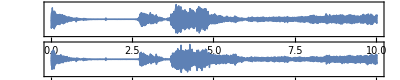

```mathematica
AudioPlot[Audio[v]]
```

Normalize the audio track and plot the resulting audio track:

```mathematica
AudioTrackApply[AudioReverse,v]
```

Video[/Users/shadi/Documents/Wolfram/Video/AudioTrackApply-61bcaaa8-4c69-46f7-bb54-3bf2a169decb.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/AudioTrackApply-61bcaaa8-4c69-46f7-bb54-3bf2a169decb.mp4Thumbnail1StandardForm

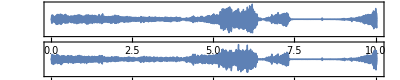

```mathematica
AudioPlot[Audio[%]]
```

### VideoMap

```mathematica
VideoMap[f, video]
VideoMap[f, video, n]
VideoMap[f, video, n, d]
```

You can do similar video track processing as VideoFrameMap:

```mathematica
VideoFrameMap[ColorNegate,v]
```

```mathematica
VideoFrameMap[ColorNegate[#]&,v]
```

Using VideoMap requires specifying the #Image argument, since the input to the function is as association with #Image, #Audio, etc. keys.

```mathematica
VideoMap[ColorNegate[#Image]&,v]
```

In addition, you can use other arguments to process video frames.

Increase the blur radius as time progresses:

```mathematica
VideoMap[Blur[#Image,5#Time]&,v]
```

Or use max audio amplitude to make video frames lighter:

```mathematica
VideoMap[Lighter[#Image,5Max[#Audio]]&,v]
```

Note: VideoMap does not copy over any additional tracks:

```mathematica
Information[v]
```

```mathematica
VideoMap[ColorNegate[#Image]&,v]//Information
```

Explicitly copy over audio data:

```mathematica
VideoMap[<|"Image"->(ColorNegate[#Image]&),"Audio"-> (#Audio&)|>,v]//Information
```

## Video Analysis

A lot of the video analysis is done on local partitions of the video. VideoMapTimeSeries returns a time series of information computed on audio or video tracks. The same information without the timestamps can be returned from VideoMapList. In addition, VideoIntervals can compute some local properties and return intervals that a desired criterion is met.

### VideoMapTimeSeries

This is renamed from VideoTimeSeries in Version 12.1. 
In addition to the name change, the input to the function is now an association with #Image, #Audio, etc. keys.

```mathematica
VideoMapTimeSeries[f, video]
VideoMapTimeSeries[f, video, n]
VideoMapTimeSeries[f, video, n, d]
```

Compute the mean of the RGB colors for every video frame and plot them:

```mathematica
v=Video["ExampleData/Caminandes.mp4"];
```

```mathematica
ts=VideoMapTimeSeries[ImageMeasurements[#Image,"Mean"]&,v]
```

TimeSeries[…]

```mathematica
DateListPlot[ts,PlotStyle->{Red,Green,Blue}]
```

-Graphics-

Compute and plot the image distance between consecutive frames:

```mathematica
v=Video["ExampleData/Caminandes.mp4"];
```

```mathematica
ts=VideoMapTimeSeries[ImageDistance@@#Image&,v,2]
```

TimeSeries[…]

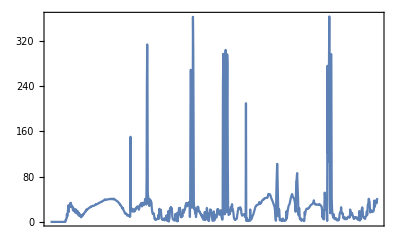

```mathematica
DateListPlot[ts,PlotRange->All]
```

Count the number of cars in each frame:

```mathematica
v=Import["http://exampledata.wolfram.com/cars.avi"];
VideoExtractFrames[v,5]
```

-Graphics-

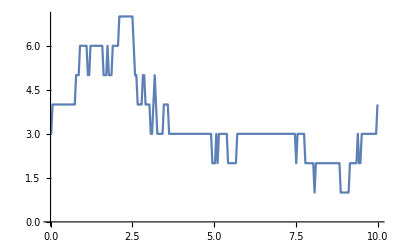

```mathematica
VideoMapTimeSeries[Length@ImageCases[#Image,Entity["Concept","Auto::p735c"]]&,v]//ListLinePlot
```

### VideoMapList

```mathematica
VideoMapList[f, video]
VideoMapList[f, video, n]
VideoMapList[f, video, n, d]
```

Compared to VideoMapTimeSeries, VideoMapList does not require that the function f return a consistent result for each evaluation. The result can be an array of arbitrary dimensions or any expression.

Compute dominant colors per frame:

```mathematica
v=Video["ExampleData/bullfinch.mkv"];
```

```mathematica
colors=VideoMapList[DominantColors[#Image]&,v];
```

Create a weighted cloud of dominant colors:

```mathematica
Tally[Flatten[colors],ColorDistance[##]<.2&]
```

{{RGBColor[0.4023895626881033, 0.4171054464216182, 0.3737577215922802],417},{RGBColor[0.48457805418480043, 0.551851206970585, 0.30476187884564654],572},{RGBColor[0.7185481314705715, 0.6627848784911373, 0.680859482525134],494},{RGBColor[0.18321303504915806, 0.21058318960554717, 0.16501212258816209],365},{RGBColor[0.5329605674161613, 0.18252718436936738, 0.14103833814032557],506},{RGBColor[0.7647155842256397, 0.3936437392345347, 0.3540444879838745],411},{RGBColor[0.32763327292252836, 0.12556567855673542, 0.09099875718114589],108},{RGBColor[0.1714054641942599, 0.19312318466275447, 0.3110922176764653],246},{RGBColor[0.6848744396361958, 0.4552382159671961, 0.5179251582552254],74},{RGBColor[0.9412148039336061, 0.6017975468321171, 0.6354378278977433],37},{RGBColor[0.9339664412681615, 0.9252741244787347, 0.9363903599737418],131},{RGBColor[0.47318290166041815, 0.5123559911998518, 0.6076985064419526],135},{RGBColor[0.8600807201017484, 0.2854825540054957, 0.22905682772986863],7},{RGBColor[0.16127090613737655, 0.08227366437730549, 0.0948079232127273],59},{RGBColor[0.45412558619460036, 0.36255300435447974, 0.20909872514648492],17},{RGBColor[0.2795712400075798, 0.34783098063285156, 0.1887707720986141],1},{RGBColor[0.6775710814475202, 0.5103878618584682, 0.4222848465394515],2},{RGBColor[0.4189252825075937, 0.33457622673877296, 0.4042261185091789],1}}

```mathematica
WordCloud[%]
```

-Graphics-

### VideoIntervals

```mathematica
VideoIntervals[video, crit]
VideoIntervals[video, crit, n]
VideoIntervals[video, crit, n, d]
```

Find video intervals with constant frames:

```mathematica
v=Video["ExampleData/Caminandes.mp4"];
```

```mathematica
VideoIntervals[v,Max[#Image]-Min[#Image]<.01&]
```

{{0.,2.125},{63.6667,65.0833},{76.0833,76.3333},{81.0833,82.875},{86.5833,88.0417}}

Find video intervals with loud audio:

```mathematica
VideoIntervals[v,First@Mean[Abs@#Audio]>.2&,Quantity[1, "Seconds"]]
```

{{13.375,14.375},{23.75,24.7917},{37.9583,39.125},{48.3333,49.4167},{48.7083,50.},{75.2917,78.4167},{79.5,81.6667}}

## Video Editing

### VideoTrim

Trim a video segment in time.

```mathematica
VideoTrim[video, t]
VideoTrim[video, {t1,t2}]
VideoTrim[video, {{t11,t12}, {t21,t22}, ...}] (* new in 12.2 *)
```

-Graphics-

```mathematica
v=Video["ExampleData/Caminandes.mp4"];
```

```mathematica
VideoTrim[v,{{10,20},{40,50}}]
```

### VideoCombine

Combine video and audio tracks.

```mathematica
VideoCombine[{video1, audio1, ...}]
```

-Graphics-

This is a video without audio:

```mathematica
VideoGenerator[ArrayPlot[CellularAutomaton[30,{{1},0},200]],2]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoGenerator-59d1e1f1-d90e-48ea-aebf-34c7ff288c3f.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoGenerator-59d1e1f1-d90e-48ea-aebf-34c7ff288c3f.mp4Thumbnail1StandardForm

Combine it with an audio object:

```mathematica
VideoCombine[{%,Audio["ExampleData/rule30.wav"]}]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoCombine-b040b208-381a-4038-9a36-b0f059893b92.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoCombine-b040b208-381a-4038-9a36-b0f059893b92.mp4Thumbnail1StandardForm

### VideoJoin

Sequentially join multiple video objects.

```mathematica
VideoJoin[video1, video2, ...]
```

-Graphics-

```mathematica
v1=VideoGenerator[ArrayPlot[CellularAutomaton[30,{{1},0},200]]]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoGenerator-065ac190-5eec-4fb0-a1f7-55a626ebdbbf.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoGenerator-065ac190-5eec-4fb0-a1f7-55a626ebdbbf.mp4Thumbnail1StandardForm

```mathematica
v2=VideoGenerator[ColorNegate@ArrayPlot[CellularAutomaton[30,{{1},0},200]]]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoGenerator-5ef51637-242c-4b9f-b9eb-066e9266dea2.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoGenerator-5ef51637-242c-4b9f-b9eb-066e9266dea2.mp4Thumbnail1StandardForm

```mathematica
VideoJoin[v1,v2,v1]
```

Video[/Users/shadi/Documents/Wolfram/Video/VideoJoin-97a99041-bb49-4789-a143-e4706220a6c6.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/Users/shadi/Documents/Wolfram/Video/VideoJoin-97a99041-bb49-4789-a143-e4706220a6c6.mp4Thumbnail1StandardForm

### VideoSplit

Split a video at the given times.

```mathematica
VideoSplit[video, {t1, t2, ...}]
```

-Graphics-

### VideoDelete

Delete the content from given time intervals.

```mathematica
VideoDelete[video, {t1,t2}]
VideoDelete[video, {{t11,t12},{t21,t22},...}]
```

-Graphics-

### VideoTranscode

Create a new video file using the specified video or audio codec, frame rate, frame resolution, audio sample rate and more.

```mathematica
VideoTranscode[video, "MP4"]
VideoTranscode[video, "Instagram"]
VideoTranscode[video, VideoEncoding->"H264", FrameRate->30, RasterSize->{1280,720}, ...]
```

```mathematica
(v=Video["ExampleData/bullfinch.mkv"])//Information
```

```mathematica
VideoTranscode[v,VideoEncoding->"H264",AudioEncoding->"AAC"]//Information
```

## Track Selection

AudioTracks in Version 12.1 is renamed to AudioTrackSelection in Version 12.2.
SubtitleTracks in Version 12.1 is renamed to SubtitleTrackSelection in Version 12.2.
VideoTracks in Version 12.1 is renamed to VideoTrackSelection in Version 12.2.

It is common for a video file to have multiple audio and subtitle tracks. It is not as common to see files with multiple video tracks, although most video containers allow for that. Track selection options can be used to specify tracks of interest.

By default, the Video object constructed from a file includes all available audio tracks:

```mathematica
Video["ExampleData/bullfinch.mkv"]//Information[#,"AudioTracks"]&
```

Include only the first audio track:

```mathematica
Video["ExampleData/bullfinch.mkv",AudioTrackSelection->1]//Information[#,"AudioTracks"]&
```

Track selection may be useful when processing only a specific track is of interest.

Here is the finch sound in the first audio track:

```mathematica
Audio[Video["ExampleData/bullfinch.mkv"]]
```

Extract and recognize the speech in the second audio track:

```mathematica
Audio[Video["ExampleData/bullfinch.mkv",AudioTrackSelection->2]]
```

```mathematica
SpeechRecognize[%]
```

## AnimatedImage

AnimatedImage is an object to display “animated images” created from a list of images or stored in formats such as PNG and GIF and display them as a dynamic animation. This object is in a sense a lightweight video and in practice is used to convey the content or the message stored in a video file in a small and fast form.

```mathematica
AnimatedImage[file]
AnimatedImage[{imag1, image2, ...}]
```

-Graphics- |  |  |  |

Create an AnimatedImage from an animated PNG:

```mathematica
a=AnimatedImage["ExampleData/pearls.png"]
```

```mathematica
Information[a]
```

Some image processing functions can be directly applied to an animated image:

```mathematica
ColorConvert[a,"Grayscale"]
```

For other processing, take images out, process, put back:

```mathematica
Image[a["ImageList"],ImageSize->50]
```

```mathematica
Image[ColorReplace[#,RGBColor[0.0028214576000536516, 0.5762718893657186, 0.9956378157416638]->RGBColor[0, 0.36, 0.21]]&/@%,ImageSize->50]
```

```mathematica
AnimatedImage[%,ImageSize->All]
```

## Improved Face Functionality

Version 12.2 introduces FaceRecognize, which can create a face classifier from a labeled set of faces. Improvements have also been made to FindFaces and FaceAlign.

Recognize if a given person is present in an image:

```mathematica
FaceRecognize[{-Graphics-->"Dad",-Graphics-->"Mom",-Graphics-->"Daughter"},-Graphics-]
```

Recognize multiple faces:

```mathematica
i=-Graphics-;
faces=FaceRecognize[{-Graphics-->"Dad",-Graphics-->"Mom",-Graphics-->"Daughter"},i,{"Image","Name","BoundingBox"}];
Dataset[faces]
```

Highlight the faces on the original image:

```mathematica
HighlightImage[i,Lookup[faces,"BoundingBox"],ImageLabels->Lookup[faces,"Name"]]
```

#### The Star Trek example…

Get some training data from the web:

```mathematica
faces=Image[#,ImageSize->30]&/@AssociationMap[Flatten[FindFaces[#,"Image"]&/@WebImageSearch["star trek "<>#]]&,{"Jean-Luc Picard","William Riker","Phillipa Louvois","Data"}]
```

<|Jean-Luc Picard→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},William Riker→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Phillipa Louvois→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Data→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

Create a face recognizer:

```mathematica
recognizer=FaceRecognize[faces]
```

ClassifierFunction[…]

Run the recognizer on each frame of this video:

```mathematica
rec=VideoMapList[recognizer[FindFaces[#Image,"Image"]]&,Video[File["/private/var/folders/8j/6jtbc26n3m7g4ljjn6z4p_kw0000gn/T/2000 promo for Star Trek - The Next Generation.ia-52254ffc-5715-4173-9714-78c2adfee0b8.mp4"],Appearance->Automatic,AudioOutputDevice->Automatic,SoundVolume->Automatic]/private/var/folders/8j/6jtbc26n3m7g4ljjn6z4p_kw0000gn/T/2000 promo for Star Trek - The Next Generation.ia-52254ffc-5715-4173-9714-78c2adfee0b8.mp4Thumbnail1StandardForm]/. m_Missing:>"Other";
Short[rec]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},«1775»,{},{Jean-Luc Picard},{Jean-Luc Picard},{Other},{},{},{},{},{},{},{},{},{},{},{}}

Plot the result of the face recognition over time:

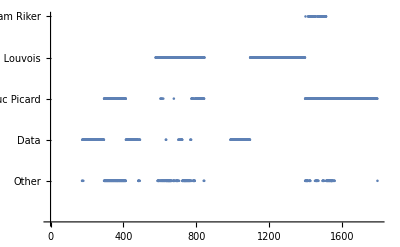

```mathematica
ListPlot[Catenate[MapIndexed[{First[#2],#1}&,ArrayComponents[rec],{2}]],]
```

## Image Scopes

Image plots and scopes are typically used to evaluate and adjust the brightness or colors of an image or frames of a video.

ImageHistogram can compute the histogram of the whole image.

ImageVectorscopePlot can be used to evaluate and adjust hue and saturation.

ImageWaveformPlot can be used to visualize image intensity/RGB waveform, where the columns correspond to image columns.

### ImageWaveformPlot

```mathematica
i=-Graphics-;
```

Overlaid image waveform of RGB channels:

```mathematica
ImageWaveformPlot[i]
```

Image waveform of the luminance channel:

```mathematica
ImageWaveformPlot[i,"L"]
```

Image waveform of channels in a row, also known as RGB parade:

```mathematica
ImageWaveformPlot[i,PlotLayout->"Row"]
```

### ImageVectorscopePlot

Vectorscope plot of an image:

```mathematica
ImageVectorscopePlot[i]
```

Use pixel colors when showing the vectorscope plot:

```mathematica
ImageVectorscopePlot[i,Appearance->"Color"]
```

Show all available appearance elements, including the skin tone axis:

```mathematica
ImageVectorscopePlot[i,Appearance->"Color",AppearanceElements->All]
```

## References

Image Processing Guide

Audio Processing Guide

Video Processing Guide

Importing & Exporting Video Tutorial

Computational Video Premieres in Wolfram Language 12.1 by Shadi Ashnai (Note: some updates to the syntax have been made since Version 12.1)